Question 4)
 ∫_0^1 u'[x]v'[x]ⅆx =  ∫_0^1 f[x]v[x]ⅆx, 
 a) W = {x(x-1), x(x-1/2)(x-1), x(x - 1/3)(x - 2/3)(x-1),x(x - 1/4)(x-1/2)(x-3/4)(x-1)}
 Let N_1 = x(x-1), N_2 = x(x-1/2)(x-1), N_3 = x(x - 1/3)(x - 2/3)(x-1), N_4= x(x - 1/4)(x-1/2)(x-3/4)(x-1)
 Now, 
 	u(x) = N_1 u_1+ N_2 u_2 + N_3 u_3+ N_4 u_4 = ∑_(i=1)^4 N_i u_i
 	∴ u’(x) =  N_1' u_1+ N_2' u_2 + N_3' u_3+ N_4' u_4 = ∑_(i=1)^4 N_i' u_i
 	∴ ∫_0^1 ( ∑ _(i=1)^4 N_i'[x]u_i)v'[x]ⅆx =  ∫_0^1 f[x]v[x]ⅆx

```mathematica
(* Basis for equation *)
Clear[u,f,n]
n = {{x(x-1), x(x-1/2)(x-1), x(x-1/3)(x-2/3)(x-1), x(x-1/4)(x-1/2)(x-3/4)(x-1)},{Sin[π x], Sin[2π x], Sin[3π x], Sin[4π x]}};

(* Unknnown coefficients Subscript[N, i] *) 
f = {Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[u, 4]}
(* Clear previous stored value *)
Clear[j];

(* Inititialize the value of j *)
j = 1;

(* Consider the basis {x(x-1), x(x-1/2)(x-1), x(x-1/3)(x-2/3)(x-1), x(x-1/4)(x-1/2)(x-3/4)(x-1)} *)
Print[Style["For the basis ",Bold]];

(* Loop #1: Solve ∫_0^1 (Subscript[N, i](x).Subscript[f, i])Subscript[N, i] ⅆx for i = 1 to 6 *)
While[j<5,
	Print[Integrate[(∑_(i=1)^4 D[n[[1,i]],x]*f[[i]])*D[n[[1,j]],x],{x,0,1}]," = ",Integrate[E^x*n[[1,j]],{x,0,1}]];
	j = j+1;
(* Loop #1: End *)
]
(* Clear the memory of variables *)
Clear[l,m]; 
l = 1;

(* Initialize null matrix *)
Nmatrix1 = {}; 

(* Creating the list of elements for Matrix *)
(* Loop #2: Start the loop for row *)
While[l<5,
	m = 1;
	
(* Loop #3: Start the loop for column *)
	While[m<5,

(* Add new element in List *)
		AppendTo[Nmatrix1,Integrate[D[n[[1,m]],x]*D[n[[1,l]],x],{x,0,1}]];
		m = m + 1;

(* Loop #3: End *)
	];
	l = l + 1;

(* Loop #2: End *)
]
(* Making matrix from list *)
Print[MatrixForm[Table[Nmatrix1[[p;;p+3]],{p,1,13,4}]]," . ",MatrixForm[ArrayReshape[f,{4,1}]] ," = ",MatrixForm[ArrayReshape[Table[Integrate[E^x*n[[1,j]],{x,0,1}],{j,1,4}],{4,1}]]]

(* Solving equation by Linearly *)
Print[MatrixForm[ArrayReshape[f,{4,1}]]," = ", MatrixForm[LinearSolve[N[Table[Nmatrix1[[p;;p+3]],{p,1,15,4}]],N[ArrayReshape[Table[Integrate[E^x*n[[1,j]],{x,0,1}],{j,1,4}],{4,1}]]]]]

(* Generating function *)
F1 = Total/@N[LinearSolve[N[Table[Nmatrix1[[p;;p+3]],{p,1,15,4}]],N[ArrayReshape[Table[Integrate[E^x*n[[1,j]],{x,0,1}],{j,1,4}],{4,1}]]]];
func1[x_] = -∑_(i=1)^4 D[D[n[[1,i]],x],x]*F1[[i]];
Print["ⅇ^x ≈ ",Simplify[func1[x]]];
```

{u_1,u_2,u_3,u_4}

For the basis

u_1/3+u_3/135 = -3+ⅇ

u_2/20+u_4/448 = 1/2 (19-7 ⅇ)

u_1/135+(10 u_3)/1701 = 4/9 (-87+32 ⅇ)

u_2/448+(43 u_4)/64512 = 1/32 (6233-2293 ⅇ)

(1/3 | 0 | 1/135 | 0
0 | 1/20 | 0 | 1/448
1/135 | 0 | 10/1701 | 0
0 | 1/448 | 0 | 43/64512) . (u_1
u_2
u_3
u_4) = (-3+ⅇ
1/2 (19-7 ⅇ)
4/9 (-87+32 ⅇ)
1/32 (6233-2293 ⅇ))

(u_1
u_2
u_3
u_4) = (-0.843607
-0.279108
-0.0696563
-0.0138962)

ⅇ^x ≈ 0.998448+1.02116 x+0.418989 x^2+0.277925 x^3

```mathematica
(* Clear previous stored value *)
Clear[j];

(* Inititialize the value of j *)
j = 1;

(* Consider the basis {{Sin[π x], Sin[2π x], Sin[3π x], Sin[4π x]}} *)
Print[Style["For the basis ",Bold]];

(* Loop #1: Solve ∫_0^1 (Subscript[N, i](x).Subscript[f, i])Subscript[N, i] ⅆx for i = 1 to 6 *)
While[j<5,
	Print[Integrate[(∑_(i=1)^4 D[n[[2,i]],x]*f[[i]])*D[n[[2,j]],x],{x,0,1}]," = ",Integrate[E^x*n[[2,j]],{x,0,1}]];
	j = j+1;
(* Loop #1: End *)
]
(* Clear the memory of variables *)
Clear[l,m]; 
l = 1;

(* Initialize null matrix *)
Nmatrix2 = {}; 

(* Creating the list of elements for Matrix *)
(* Loop #2: Start the loop for row *)
While[l<5,
	m = 1;
	
(* Loop #3: Start the loop for column *)
	While[m<5,

(* Add new element in List *)
		AppendTo[Nmatrix2,Integrate[D[n[[2,m]],x]*D[n[[2,l]],x],{x,0,1}]];
		m = m + 1;

(* Loop #3: End *)
	];
	l = l + 1;

(* Loop #2: End *)
]
(* Making matrix from list *)
Print[MatrixForm[Table[Nmatrix2[[p;;p+3]],{p,1,13,4}]]," . ",MatrixForm[ArrayReshape[f,{4,1}]] ," = ",MatrixForm[ArrayReshape[Table[Integrate[E^x*n[[2,j]],{x,0,1}],{j,1,4}],{4,1}]]]

(* Solving equation by Linearly *)
Print[MatrixForm[ArrayReshape[f,{4,1}]]," = ", MatrixForm[LinearSolve[N[Table[Nmatrix2[[p;;p+3]],{p,1,15,4}]],N[ArrayReshape[Table[Integrate[E^x*n[[2,j]],{x,0,1}],{j,1,4}],{4,1}]]]]]

(* Generating function *)
F2 = Total/@N[LinearSolve[N[Table[Nmatrix2[[p;;p+3]],{p,1,15,4}]],N[ArrayReshape[Table[Integrate[E^x*n[[2,j]],{x,0,1}],{j,1,4}],{4,1}]]]];
func2[x_] = -∑_(i=1)^4 D[D[n[[2,i]],x],x]*F2[[i]];
Print["ⅇ^x ≈ ",func2[x]];
```

For the basis

(π^2 u_1)/2 = ((1+ⅇ) π)/(1+π^2)

2 π^2 u_2 = -(2 (-1+ⅇ) π)/(1+4 π^2)

(9 π^2 u_3)/2 = (3 (1+ⅇ) π)/(1+9 π^2)

8 π^2 u_4 = -(4 (-1+ⅇ) π)/(1+16 π^2)

(π^2/2 | 0 | 0 | 0
0 | 2 π^2 | 0 | 0
0 | 0 | (9 π^2)/2 | 0
0 | 0 | 0 | 8 π^2) . (u_1
u_2
u_3
u_4) = (((1+ⅇ) π)/(1+π^2)
-(2 (-1+ⅇ) π)/(1+4 π^2)
(3 (1+ⅇ) π)/(1+9 π^2)
-(4 (-1+ⅇ) π)/(1+16 π^2))

(u_1
u_2
u_3
u_4) = (0.217775
-0.013512
0.00878409
-0.00172089)

ⅇ^x ≈ 2.14936 Sin[π x]-0.533434 Sin[2 π x]+0.78026 Sin[3 π x]-0.271752 Sin[4 π x]

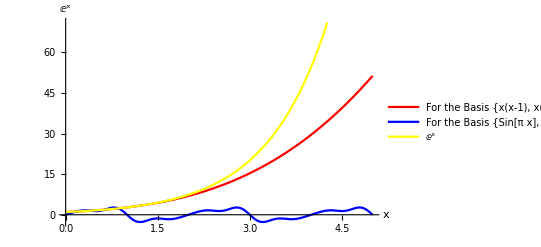

```mathematica
Plot[{func1[x],func2[x],E^x},{x,0,5},PlotStyle->{Red,Blue,Yellow},
PlotLegends->{"For the Basis {x(x-1), x(x-1/2)(x-1), x(x-1/3)(x-2/3)(x-1), x(x-1/4)(x-1/2)(x-3/4)(x-1)}","For the Basis {Sin[π x], Sin[2π x], Sin[3π x], Sin[4π x]}","ⅇ^x"},AxesLabel->{x,ⅇ^x}]
```

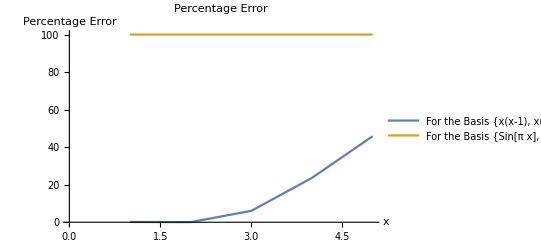

```mathematica
(* Percentage Error *)
i = 1;
err1 = {};
err2 = {};
While[i<6,
AppendTo[err1, Abs[(E^(i-1)- func1[i-1])/E^(i-1)]*100.];
AppendTo[err2, Abs[(E^(i-1) - func2[i-1])/E^(i-1)]*100.];

i = i+1;
]
ListLinePlot[{err1,err2},PlotLegends->{"For the Basis {x(x-1), x(x-1/2)(x-1), x(x-1/3)(x-2/3)(x-1), x(x-1/4)(x-1/2)(x-3/4)(x-1)}","For the Basis {Sin[π x], Sin[2π x], Sin[3π x], Sin[4π x]}"},
PlotLabel->"Percentage Error",AxesLabel->{x,"Percentage Error"}]
```